# Analiza korelacije števila ilegalnih migracij glede na politično stranko v Republiki Sloveniji za obdobje 2017-2024

```mathematica
(*Podatki*)leta=Range[2017,2024];
migracije={1930,9149,16099,14592,10067,32024,60587,46192};
stranke={"SMC","SMC","LMŠ","LMŠ","SDS","SDS","Gibanje Svoboda","Gibanje Svoboda"};
```

```mathematica
(*Stolpični diagram števila migracij po letih*)grafLeta=BarChart[migracije,ChartLabels->Placed[leta,Below],ChartStyle->ColorData[97,"ColorList"],AxesLabel->{"Leto","Število ilegalnih migracij"},PlotLabel->"Število ilegalnih migracij v RS po letih",ImageSize->Large];
```

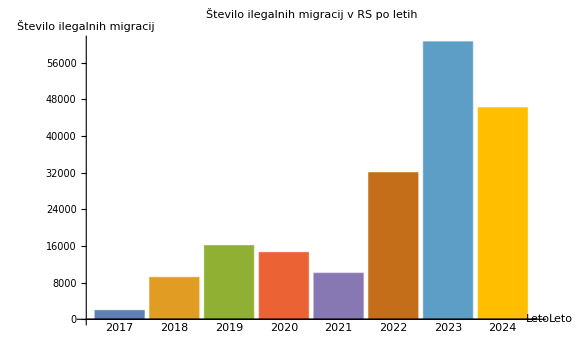

```mathematica
%72
```

```mathematica
(*Združevanje podatkov po strankah*)skupnoPoStrankah=Total/@GatherBy[Transpose[{stranke,migracije}],First][[All,All,2]];
edinstveneStranke=DeleteDuplicates[stranke];
```

```mathematica
{11079,30691,42091,106779}
```

{11079,30691,42091,106779}

```mathematica
(*Seznam let in njim pripadajoče število migracij*)
```

```mathematica
Map[Function[{pair},ToString[pair[[1]]]<>": "<>ToString[pair[[2]]]],Transpose[{leta,migracije}]]
```

{2017: 1930,2018: 9149,2019: 16099,2020: 14592,2021: 10067,2022: 32024,2023: 60587,2024: 46192}

```mathematica
(*Stolpični diagram števila migracij po strankah*)grafStranke=BarChart[skupnoPoStrankah,ChartLabels->Placed[edinstveneStranke,Below],ChartStyle->ColorData[112,"ColorList"],AxesLabel->{"Stranka","Skupno število ilegalnih migracij"},PlotLabel->"Skupno število ilegalnih migracij glede na vodilno stranko",ImageSize->Large];
```

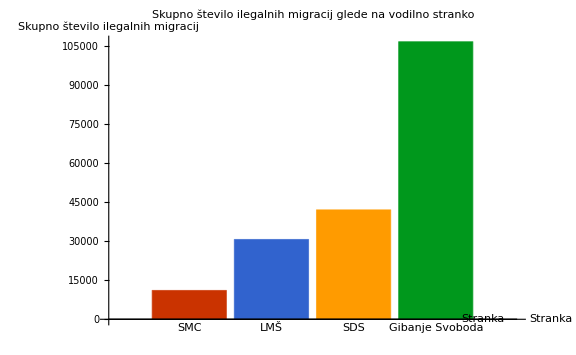

```mathematica
%77
```

```mathematica
(*Tortni diagram deleža migracij po strankah*)grafTorta=PieChart[skupnoPoStrankah,ChartLabels->edinstveneStranke,ChartStyle->"Pastel",PlotLabel->"Delež ilegalnih migracij po strankah",ImageSize->Large];
```

```mathematica
%79
```

-Graphics-

```mathematica
(*Tabela:leto,migracije,stranka*)tabelaLetoStranka=Grid[Prepend[Transpose[{leta,migracije,stranke}],{"Leto","Število ilegalnih migracij","Vodilna stranka"}],Frame->All];
```

```mathematica
%81
```

Leto | Število ilegalnih migracij | Vodilna stranka
2017 | 1930 | SMC
2018 | 9149 | SMC
2019 | 16099 | LMŠ
2020 | 14592 | LMŠ
2021 | 10067 | SDS
2022 | 32024 | SDS
2023 | 60587 | Gibanje Svoboda
2024 | 46192 | Gibanje Svoboda

```mathematica
(*Sprememba števila migracij po letih v procentih*)
```

```mathematica
(*Od leta in do leta*)
odLet=Most[leta];
doLet=Rest[leta];

(*Izračun odstotnih sprememb kot decimalnih števil,zaokroženih na 2 decimali*)
spremembe=Table[Round[100.0*(migracije[[i+1]]-migracije[[i]])/migracije[[i]],0.01],{i,Length[migracije]-1}];

(*Pretvori v nize s + ali - predznakom*)
spremembeStr=Map[If[#>=0,"+"<>ToString[#],ToString[#]]&,spremembe];

(*Vodilna stranka v drugem letu obdobja*)
strankeObdobij=Rest[stranke];

(*Ustvari tabelo*)
tabelaProcentSprememb=Grid[Prepend[Transpose[{odLet,doLet,spremembeStr,strankeObdobij}],{"Od leta","Do leta","Sprememba (%)","Vodilna stranka"}],Frame->All,Background->{None,{LightGray,{White}}}];

(*Prikaži tabelo*)
tabelaProcentSprememb
```

Od leta | Do leta | Sprememba (%) | Vodilna stranka
2017 | 2018 | +374.04 | SMC
2018 | 2019 | +75.96 | LMŠ
2019 | 2020 | -9.36 | LMŠ
2020 | 2021 | -31.01 | SDS
2021 | 2022 | +218.11 | SDS
2022 | 2023 | +89.19 | Gibanje Svoboda
2023 | 2024 | -23.76 | Gibanje Svoboda